## Importazione matrici algebriche

```mathematica
SetDirectory[NotebookDirectory[]];
algebra=Import["algebra.m","ExpressionList"][[1]];
```

```mathematica
Length[algebra] (* deve valere 2 *)
```

2

```mathematica
Length[algebra[[1]]] (* deve valere 6 *)
```

6

```mathematica
Length[algebra[[2]]] (* deve valere 4 *)
```

4

```mathematica
{s0[k_],s1[k_,a_],s2[k_,a_,b_],s3[k_,a_,b_,c_],ee[k_,a_,b_,c_,d_],centro[k_,a_,b_,c_,d_]}=algebra[[1]];
{sup0[k_],sup1[k_,a_],eesup[k_,a_,b_],centrosup[k_,a_,b_]}=algebra[[2]];
```

```mathematica
rotDH[α_,a_,d_,θ_]:={
{Cos[θ],-Cos[α] Sin[θ], Sin[α]Sin[θ],a Cos[θ]},
{Sin[θ],Cos[α]Cos[θ],-Sin[α]Cos[θ],a Sin[θ]},
{0,Sin[α],Cos[α],d},
{0,0,0,1}}
```

## Parte Superiore

## Centro (di ogni spicchio)

```mathematica
centrosup[k,θ1,θ2]//MatrixForm
```

(-Sin[gamma+1/6 (π+2 k π)] Sin[delta+epsilon+θ1+θ2] | Cos[gamma+1/6 (π+2 k π)] | -Cos[delta+epsilon+θ1+θ2] Sin[gamma+1/6 (π+2 k π)] | 1/2 Sin[gamma+1/6 (π+2 k π)] (d1+2 ls1 Cos[θ1]+2 xsup Cos[θ1+θ2]+2 r2 Cos[delta+θ1+θ2]-2 ysup Sin[θ1+θ2])
Cos[gamma+1/6 (π+2 k π)] Sin[delta+epsilon+θ1+θ2] | Sin[gamma+1/6 (π+2 k π)] | Cos[gamma+1/6 (π+2 k π)] Cos[delta+epsilon+θ1+θ2] | -1/2 Cos[gamma+1/6 (π+2 k π)] (d1+2 ls1 Cos[θ1]+2 xsup Cos[θ1+θ2]+2 r2 Cos[delta+θ1+θ2]-2 ysup Sin[θ1+θ2])
Cos[delta+epsilon+θ1+θ2] | 0 | -Sin[delta+epsilon+θ1+θ2] | h1+ysup Cos[θ1+θ2]+ls1 Sin[θ1]+xsup Sin[θ1+θ2]+r2 Sin[delta+θ1+θ2]
0 | 0 | 0 | 1)

Mi metto sul piano di lavoro del manipolatore (piano su cui si muove il centro della shell superiore)

```mathematica
Simplify[rotDH[0,0,0,-gamma].centrosup[1,θ1,θ2]]//MatrixForm
```

(-Sin[delta+epsilon+θ1+θ2] | 0 | -Cos[delta+epsilon+θ1+θ2] | d1/2+ls1 Cos[θ1]+xsup Cos[θ1+θ2]+r2 Cos[delta+θ1+θ2]-ysup Sin[θ1+θ2]
0 | 1 | 0 | 0
Cos[delta+epsilon+θ1+θ2] | 0 | -Sin[delta+epsilon+θ1+θ2] | h1+ysup Cos[θ1+θ2]+ls1 Sin[θ1]+xsup Sin[θ1+θ2]+r2 Sin[delta+θ1+θ2]
0 | 0 | 0 | 1)

```mathematica
verticale=Solve[delta+epsilon+θ1+θ2==3Pi/2,θ2]
```

{{θ2→1/2 (-2 delta-2 epsilon+3 π-2 θ1)}}

```mathematica
Simplify[Evaluate[centrosup[1,θ1,θ2]/. verticale]][[1]]//MatrixForm
```

(Cos[gamma] | -Sin[gamma] | 0 | 1/2 Cos[gamma] (d1+2 ysup Cos[delta+epsilon]+2 ls1 Cos[θ1]-2 r2 Sin[epsilon]-2 xsup Sin[delta+epsilon])
Sin[gamma] | Cos[gamma] | 0 | 1/2 (d1+2 ysup Cos[delta+epsilon]+2 ls1 Cos[θ1]-2 r2 Sin[epsilon]-2 xsup Sin[delta+epsilon]) Sin[gamma]
0 | 0 | 1 | h1-r2 Cos[epsilon]-xsup Cos[delta+epsilon]-ysup Sin[delta+epsilon]+ls1 Sin[θ1]
0 | 0 | 0 | 1)

```mathematica
sommasup:=-angle-delta-epsilon
sigma1:=ArcSin[(-h1+height-ysup Cos[sommasup]-xsup Sin[sommasup]-r2 Sin[delta+sommasup])/ls1]
sigma2:=sommasup-sigma1
```

```mathematica
Simplify[Evaluate[centrosup[k,sigma1,sigma2]]]//MatrixForm
```

(Sin[angle] Sin[gamma+1/6 (π+2 k π)] | Cos[gamma+1/6 (π+2 k π)] | -Cos[angle] Sin[gamma+1/6 (π+2 k π)] | 1/2 (d1+2 r2 Cos[angle+epsilon]+2 xsup Cos[angle+delta+epsilon]+2 ysup Sin[angle+delta+epsilon]+2 ls1 √(1-(-h1+height-ysup Cos[angle+delta+epsilon]+r2 Sin[angle+epsilon]+xsup Sin[angle+delta+epsilon])^2/ls1^2)) Sin[gamma+1/6 (π+2 k π)]
-Cos[gamma+1/6 (π+2 k π)] Sin[angle] | Sin[gamma+1/6 (π+2 k π)] | Cos[angle] Cos[gamma+1/6 (π+2 k π)] | -1/2 Cos[gamma+1/6 (π+2 k π)] (d1+2 r2 Cos[angle+epsilon]+2 xsup Cos[angle+delta+epsilon]+2 ysup Sin[angle+delta+epsilon]+2 ls1 √(1-(-h1+height-ysup Cos[angle+delta+epsilon]+r2 Sin[angle+epsilon]+xsup Sin[angle+delta+epsilon])^2/ls1^2))
Cos[angle] | 0 | Sin[angle] | height
0 | 0 | 0 | 1)

```mathematica
With[{angle=Pi/2},Evaluate[centrosup[1,sigma1,sigma2]]]//MatrixForm
```

(Cos[gamma] | -Sin[gamma] | 0 | 1/2 Cos[gamma] (d1+2 ysup Cos[delta+epsilon]-2 r2 Sin[epsilon]-2 xsup Sin[delta+epsilon]+2 ls1 √(1-(-h1+height+r2 Cos[epsilon]+xsup Cos[delta+epsilon]+ysup Sin[delta+epsilon])^2/ls1^2))
Sin[gamma] | Cos[gamma] | 0 | 1/2 (d1+2 ysup Cos[delta+epsilon]-2 r2 Sin[epsilon]-2 xsup Sin[delta+epsilon]+2 ls1 √(1-(-h1+height+r2 Cos[epsilon]+xsup Cos[delta+epsilon]+ysup Sin[delta+epsilon])^2/ls1^2)) Sin[gamma]
0 | 0 | 1 | height
0 | 0 | 0 | 1)

Cerco le soluzioni per cui la shell è chiusa, le condizioni sono angle = -Pi/2 e x = 0

```mathematica
chiusura=Solve[d1+2 ysup Cos[delta+epsilon]-2 r2 Sin[epsilon]-2 xsup Sin[delta+epsilon]+2 ls1 √(1-1/ls1^2(-h1+height+r2 Cos[epsilon]+xsup Cos[delta+epsilon]+ysup Sin[delta+epsilon])^2)==0,height]
```

{{height→1/2 (2 h1-2 r2 Cos[epsilon]-2 xsup Cos[delta+epsilon]-2 ysup Sin[delta+epsilon]-√(-d1^2+4 ls1^2-2 r2^2-2 xsup^2-2 ysup^2-4 r2 xsup Cos[delta]+2 r2^2 Cos[2 epsilon]-4 d1 ysup Cos[delta+epsilon]+4 r2 xsup Cos[delta+2 epsilon]+2 xsup^2 Cos[2 delta+2 epsilon]-2 ysup^2 Cos[2 delta+2 epsilon]-4 r2 ysup Sin[delta]+4 d1 r2 Sin[epsilon]+4 d1 xsup Sin[delta+epsilon]+4 r2 ysup Sin[delta+2 epsilon]+4 xsup ysup Sin[2 delta+2 epsilon]))},{height→1/2 (2 h1-2 r2 Cos[epsilon]-2 xsup Cos[delta+epsilon]-2 ysup Sin[delta+epsilon]+√(-d1^2+4 ls1^2-2 r2^2-2 xsup^2-2 ysup^2-4 r2 xsup Cos[delta]+2 r2^2 Cos[2 epsilon]-4 d1 ysup Cos[delta+epsilon]+4 r2 xsup Cos[delta+2 epsilon]+2 xsup^2 Cos[2 delta+2 epsilon]-2 ysup^2 Cos[2 delta+2 epsilon]-4 r2 ysup Sin[delta]+4 d1 r2 Sin[epsilon]+4 d1 xsup Sin[delta+epsilon]+4 r2 ysup Sin[delta+2 epsilon]+4 xsup ysup Sin[2 delta+2 epsilon]))}}

```mathematica
gomitobasso=First[chiusura];
gomitoalto=Last[chiusura];
```

```mathematica
(* gambe inferiori *)
h0=-29;  (* distanza fra il piano medio del robot (metà middle chassis) e il piano medio della gamba 1 inferiore *)
d0=132;  (* doppio dell'interasse fra le ruote dentate *)
l1=120  ;(* lunghezza gamba 1 inferiore (distanza fra i due assi di rotazione) *)
h2=- 24.25; (* distanza (in verticale) fra il piano medio della gamba 1 e l'asse di rotazione del primo motore collegato alla gamba 2 *)
l2=33.5;(* distanza minima fra gli assi di rotazione dei due motori *)
h3=24.25 ; (* distanza fra l'asse (verticale) del giunto 2 e il piano medio della gamba 2........é stato aggiunto nella matrice s3 per rispettare la convenione di DH, ma si può anche ottenere con una traslazione lungo y come mostrato nel calcolo di O2a, O2b e O2c *)
l3=40 ;(* lunghezza gamba 2 *)
l4=112 ;(* distanza fra l'asse dell'ultimo motore e l'end effector vero e proprio.......essendo formato da parti curve e più complesse non è possibile conoscerlo a priori ma deve essere misurato, è compreso fra 120 e 125 mm *)
xinf=42;(* distanza fra l'asse dell'ultimo motore e lo spigolo "a monte" (cioè più vicino al centro del robot) del piano di contatto fra end effector e bottom shell, anche questo è affetto la leggere incertezza (+- 0.2 mm) *)
yinf=-23.6 ;(* come sopra ma in direzione y, anche qui si ha incertezza *)
r1=150;(* distanza fra lo spigolo e il centro della shell *)
alpha=85°+11°; (* angolo di inclinazione del il piano di contatto ee-bs rispetto al raggio r1 + angolo piano - asse x *)
beta=38° ;(* angolo di inclinazione di r1 rispetto alla verticale quando il robot è chiuso *)

(* gambe superiori *)
d1=153.5  ;(* distanza fra gli assi di due motori opposti *)
h1=63.5 ;(* distanza verticale fra il piano medio del robot e l'asse di rotazione del primo motore *)
ls1=65; (* lunghezza gamba superiore *)
ls2=100 ;(* DA RIVEDERE! Posizione dell'end effector nella parte superiore *)
gamma=-12°; (* angolo di rotazione fra midlle chassis e upper chassis (le 6 gambe non sono allineate *)
delta=90° ;(* angolo corrispondente ad alpha nella parte superiore *)
epsilon=75°; (* angolo corrispondente a beta nella parte superiore *)
xsup=10.75 ;(* come sopra *)
ysup=-19 ;(* come sopra *)
r2=150;(* come sopra*)

r=330/2; (* raggio esterno della sfera *)
```

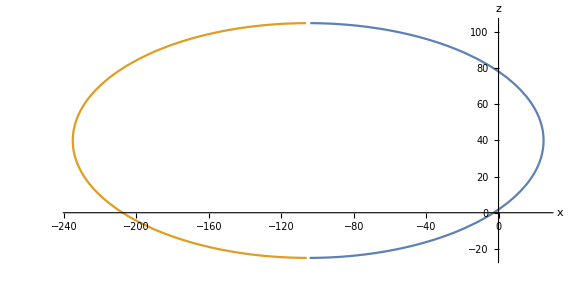

```mathematica
ParametricPlot[{{d1+2 ysup Cos[delta+epsilon]-2 r2 Sin[epsilon]-2 xsup Sin[delta+epsilon]+2 ls1 √(1-1/ls1^2(-h1+height+r2 Cos[epsilon]+xsup Cos[delta+epsilon]+ysup Sin[delta+epsilon])^2),height},{d1+2 ysup Cos[delta+epsilon]-2 r2 Sin[epsilon]-2 xsup Sin[delta+epsilon]-2 ls1 √(1-1/ls1^2(-h1+height+r2 Cos[epsilon]+xsup Cos[delta+epsilon]+ysup Sin[delta+epsilon])^2),height}},{height,-50,120},AspectRatio->Automatic,ImageSize->Large,AxesLabel->{"x","z"},LabelStyle->"Author"]
```

Questo è il percorso fatto dal centro della shell al variare dell’altezza, imponendo che l’asse rimanga sempre veriticale.
Si vedono le due soluzioni “gomito alto” e “gomito basso”, corrispondenti alle due intersezioni con l’asse x = 0.

```mathematica
gomitobasso
gomitoalto
```

{height→1.74827}

{height→78.2085}

## Parte Inferiore

## End effector

```mathematica
(* cancello i valori numerici delle costanti *)
Clear["x*","y*","l*","h*","d*",alpha,beta,gamma,delta,epsilon,r1,r2,mov]
```

```mathematica
ee[k,θ1,θ2,θ3,θ4]//MatrixForm
```

(Cos[θ3+θ4] Sin[1/6 (π+2 k π)+θ1+θ2] | -Sin[1/6 (π+2 k π)+θ1+θ2] Sin[θ3+θ4] | Cos[1/6 (π+2 k π)+θ1+θ2] | h3 Cos[1/6 (1+2 k) π+θ1+θ2]+1/2 d0 Sin[1/6 (π+2 k π)]+l1 Sin[1/6 (π+2 k π)+θ1]+(l2+l3 Cos[θ3]+l4 Cos[θ3+θ4]) Sin[1/6 (1+2 k) π+θ1+θ2]
-Cos[1/6 (π+2 k π)+θ1+θ2] Cos[θ3+θ4] | Cos[1/6 (π+2 k π)+θ1+θ2] Sin[θ3+θ4] | Sin[1/6 (π+2 k π)+θ1+θ2] | -1/2 d0 Cos[1/6 (π+2 k π)]-l1 Cos[1/6 (π+2 k π)+θ1]-Cos[1/6 (π+2 k π)+θ1+θ2] (l2+l3 Cos[θ3]+l4 Cos[θ3+θ4])+h3 Sin[1/6 (π+2 k π)+θ1+θ2]
-Sin[θ3+θ4] | -Cos[θ3+θ4] | 0 | h0+h2-l3 Sin[θ3]-l4 Sin[θ3+θ4]
0 | 0 | 0 | 1)

```mathematica
ee[1,0,θ2,θ3,θ4]//MatrixForm
```

(Cos[θ2] Cos[θ3+θ4] | -Cos[θ2] Sin[θ3+θ4] | -Sin[θ2] | d0/2+l1+Cos[θ2] (l2+l3 Cos[θ3]+l4 Cos[θ3+θ4])-h3 Sin[θ2]
Cos[θ3+θ4] Sin[θ2] | -Sin[θ2] Sin[θ3+θ4] | Cos[θ2] | h3 Cos[θ2]+(l2+l3 Cos[θ3]+l4 Cos[θ3+θ4]) Sin[θ2]
-Sin[θ3+θ4] | -Cos[θ3+θ4] | 0 | h0+h2-l3 Sin[θ3]-l4 Sin[θ3+θ4]
0 | 0 | 0 | 1)

```mathematica
lpm:={{1,0,0,d0/2+l1},{0,1,0,0},{0,0,1,h0+h2},{0,0,0,1}}
rpm:={{1,0,0,0},{0,1,0,0},{0,0,1,-h3},{0,0,0,1}}
Simplify[Inverse[lpm].ee[k,0,θ2,θ3,θ4].rpm]//MatrixForm
```

(Cos[θ3+θ4] Sin[1/6 (1+2 k) π+θ2] | -Sin[1/6 (1+2 k) π+θ2] Sin[θ3+θ4] | Cos[1/6 (1+2 k) π+θ2] | -d0/2-l1+(d0/2+l1) Sin[1/6 (π+2 k π)]+(l2+l3 Cos[θ3]+l4 Cos[θ3+θ4]) Sin[1/6 (1+2 k) π+θ2]
-Cos[1/6 (1+2 k) π+θ2] Cos[θ3+θ4] | Cos[1/6 (1+2 k) π+θ2] Sin[θ3+θ4] | Sin[1/6 (1+2 k) π+θ2] | -1/2 (d0+2 l1) Cos[1/6 (π+2 k π)]-Cos[1/6 (1+2 k) π+θ2] (l2+l3 Cos[θ3]+l4 Cos[θ3+θ4])
-Sin[θ3+θ4] | -Cos[θ3+θ4] | 0 | -l3 Sin[θ3]-l4 Sin[θ3+θ4]
0 | 0 | 0 | 1)

```mathematica
simple=Simplify[Inverse[lpm].ee[1,0,θ2,θ3,θ4].rpm];
simple//MatrixForm
```

(Cos[θ2] Cos[θ3+θ4] | -Cos[θ2] Sin[θ3+θ4] | -Sin[θ2] | Cos[θ2] (l2+l3 Cos[θ3]+l4 Cos[θ3+θ4])
Cos[θ3+θ4] Sin[θ2] | -Sin[θ2] Sin[θ3+θ4] | Cos[θ2] | (l2+l3 Cos[θ3]+l4 Cos[θ3+θ4]) Sin[θ2]
-Sin[θ3+θ4] | -Cos[θ3+θ4] | 0 | -l3 Sin[θ3]-l4 Sin[θ3+θ4]
0 | 0 | 0 | 1)

Calcolo θ2

```mathematica
q2[x_,y_]:=ArcTan[y/x]
Simplify[Expand[q2[simple[[1,4]],simple[[2,4]]]]]
```

ArcTan[Tan[θ2]]

Mathematica, non conoscendo il range di θ2 lascia indicato Arctan[Tan[θ2]] perché il risultato non è necessariamente θ2. Per ottenere θ2 devo aggiungere delle condizioni.

```mathematica
Simplify[Expand[q2[simple[[1,4]],simple[[2,4]]]],-Pi/2<θ2<Pi/2]
```

θ2

Conoscendo θ2 posso calcolare θ4 dalla seguente espressione.

```mathematica
Simplify[Expand[(simple[[1,4]]-l2 Cos[θ2])^2+(simple[[2,4]]-l2 Sin[θ2])^2+simple[[3,4]]^2]]
```

l3^2+l4^2+2 l3 l4 Cos[θ4]

```mathematica
q4[x_,y_,z_]:=ArcCos[((x-l2 Cos[q2[x,y]])^2+(y-l2 Sin[q2[x,y]])^2+z^2-l3^2-l4^2)/(2l3 l4)]
```

```mathematica
Simplify[Expand[q4[simple[[1,4]],simple[[2,4]],simple[[3,4]]]],-Pi/2<θ2<Pi/2&&0<θ4<Pi]
```

θ4

A questo punto calcolo θ3

```mathematica
Simplify[Expand[Sqrt[(simple[[1,4]]-l2 Cos[θ2])^2+(simple[[2,4]]-l2 Sin[θ2])^2]*(l3+l4 Cos[θ4])-simple[[3,4]]l4 Sin[θ4]],l3 Cos[θ3]+l4 Cos[θ3+θ4]>0]
```

Cos[θ3] (l3^2+l4^2+2 l3 l4 Cos[θ4])

```mathematica
q3[x_,y_,z_]:=ArcCos[
(Sqrt[(x - l2*Cos[q2[x,y]])^2+ (y - l2*Sin[q2[x,y]])^2]*(l3 + l4*Cos[q4[x,y,z]])-z*l4*Sin[q4[x,y,z]])/((x-l2 Cos[q2[x,y]])^2+(y-l2 Sin[q2[x,y]])^2+z^2)]
```

```mathematica
Simplify[Expand[q3[simple[[1,4]],simple[[2,4]],simple[[3,4]]]],-Pi/2<θ2<Pi/2&&0<θ4<Pi&&l3 Cos[θ3]+l4 Cos[θ3+θ4]>0]
```

ArcCos[Cos[θ3]]

Vado a ricomporre la matrice ee

```mathematica
Simplify[Evaluate[Inverse[lpm].ee[1,0,q2[x,y],q3[x,y,z],q4[x,y,z]].rpm],x>0&&z<0]//MatrixForm
```

((x Cos[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]])/(√(x^2+y^2)) | -(x Sin[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]])/(√(x^2+y^2)) | -y/(√(x^2+y^2)) | (x (l2+(l3 ((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2))))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)+l4 Cos[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]]))/(√(x^2+y^2))
(y Cos[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]])/(√(x^2+y^2)) | -(y Sin[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]])/(√(x^2+y^2)) | x/(√(x^2+y^2)) | (y (l2+(l3 ((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2))))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)+l4 Cos[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]]))/(√(x^2+y^2))
-Sin[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]] | -Cos[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]] | 0 | -l3 √(1-((-(√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)+l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))^2)/((l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2))-l4 Sin[ArcCos[(l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)/(2 l3 l4)]+ArcCos[((√(l2^2+x^2+y^2-2 l2 √(x^2+y^2)) (l2^2+l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2))/(2 l3)-l4 z √(1-((l2^2-l3^2-l4^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)^2)/(4 l3^2 l4^2)))/(l2^2+x^2+y^2-2 l2 √(x^2+y^2)+z^2)]]
0 | 0 | 0 | 1)

## Centro (di ogni spicchio)

```mathematica
(* cancello i valori numerici delle costanti *)
Clear["x*","y*","l*","h*","d*",alpha,beta,gamma,delta,epsilon,r, r1,r2,mov]
```

```mathematica
centro[k,θ1,θ2,θ3,θ4]//MatrixForm
```

(-Sin[1/6 (1+2 k) π+θ1+θ2] Sin[alpha+beta+θ3+θ4] | Cos[1/6 (1+2 k) π+θ1+θ2] | Cos[alpha+beta+θ3+θ4] Sin[1/6 (1+2 k) π+θ1+θ2] | h3 Cos[1/6 (1+2 k) π+θ1+θ2]+1/2 d0 Sin[1/6 (π+2 k π)]+l1 Sin[1/6 (1+2 k) π+θ1]+Sin[1/6 (1+2 k) π+θ1+θ2] (l2+l3 Cos[θ3]+xinf Cos[θ3+θ4]+r1 Cos[alpha+θ3+θ4]-yinf Sin[θ3+θ4])
Cos[1/6 (1+2 k) π+θ1+θ2] Sin[alpha+beta+θ3+θ4] | Sin[1/6 (1+2 k) π+θ1+θ2] | -Cos[1/6 (1+2 k) π+θ1+θ2] Cos[alpha+beta+θ3+θ4] | -1/2 d0 Cos[1/6 (π+2 k π)]-l1 Cos[1/6 (1+2 k) π+θ1]+h3 Sin[1/6 (1+2 k) π+θ1+θ2]-Cos[1/6 (1+2 k) π+θ1+θ2] (l2+l3 Cos[θ3]+xinf Cos[θ3+θ4]+r1 Cos[alpha+θ3+θ4]-yinf Sin[θ3+θ4])
-Cos[alpha+beta+θ3+θ4] | 0 | -Sin[alpha+beta+θ3+θ4] | h0+h2-yinf Cos[θ3+θ4]-l3 Sin[θ3]-xinf Sin[θ3+θ4]-r1 Sin[alpha+θ3+θ4]
0 | 0 | 0 | 1)

Per chiudere il robot a sfera le condizioni sono: 
θ1+θ2 = -72°
alpha+beta+θ3+θ4+90° = 360°
x = 0
y = 0

Parto a risolvere dall’elemento 24 (posizione y)

```mathematica
Reduce[h3 Cos[somma]+l1 Sin[θ1]+mov Sin[somma]==0&&h3>0&&l1>0&&Sin[θ1]<0,somma,Reals]
```

h3>0&&l1>0&&((C[1]∈ℤ&&Sin[θ1]==-√((h3^2+mov^2)/l1^2)&&somma==2 ArcTan[mov/(h3+l1 √((h3^2+mov^2)/l1^2))]+2 π C[1])||(C[1]∈ℤ&&-√((h3^2+mov^2)/l1^2)<Sin[θ1]<0&&(somma==2 ArcTan[(mov-h3 √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2)+l1 Sin[θ1] √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2))/(h3-l1 Sin[θ1])]+2 π C[1]||somma==2 ArcTan[(mov+h3 √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2)-l1 Sin[θ1] √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2))/(h3-l1 Sin[θ1])]+2 π C[1])))

Sostituisco l’equzione ottenuta nella 14 (posizione x) e trovo “mov” (per ora considero soltanto il secondo caso, il caso in cui sin(θ1) = - √(h3^2+mov^2)/l1^2 verrà discusso dopo).
Sia che prenda la prima o la seconda soluzione il risultato è il seguente

```mathematica
Solve[d0/2+l1 Cos[θ1]-h3 Sin[2 ArcTan[(mov-h3 √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2)+l1 Sin[θ1] √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2))/(h3-l1 Sin[θ1])]]
+mov Cos[2 ArcTan[(mov-h3 √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2)+l1 Sin[θ1] √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2))/(h3-l1 Sin[θ1])]]==0,mov]
```

{{mov→-1/2 √(d0^2-4 h3^2+4 d0 l1 Cos[θ1]+4 l1^2 Cos[θ1]^2+4 l1^2 Sin[θ1]^2)},{mov→1/2 √(d0^2-4 h3^2+4 d0 l1 Cos[θ1]+4 l1^2 Cos[θ1]^2+4 l1^2 Sin[θ1]^2)}}

La soluzione corretta è quella negativa (devo tornare indietro rispetto al giunto θ2)

A questo punto vado a risolvere per θ3 e θ4, con la regola che θ3 + θ4 ==3/2 π - alpha - beta

```mathematica
Reduce[-1/2 √(d0^2-4 h3^2+4 d0 l1 Cos[θ1]+4 l1^2 Cos[θ1]^2+4 l1^2 Sin[θ1]^2)==l2+l3 Cos[θ3]+xinf Cos[3Pi/2-alpha-beta]+r1 Cos[3Pi/2-beta]-yinf Sin[3Pi/2-alpha-beta]&&r1>0&&l3>0&&l2>0&&xinf>0&&yinf<0,θ3]
```

C[1]∈ℤ&&l2>0&&l3>0&&r1>0&&xinf>0&&yinf<0&&(θ3==-ArcCos[(-2 l2-2 yinf Cos[alpha+beta]+2 r1 Sin[beta]+2 xinf Sin[alpha+beta]-√(d0^2-4 h3^2+4 d0 l1 Cos[θ1]+4 l1^2 Cos[θ1]^2+4 l1^2 Sin[θ1]^2))/(2 l3)]+2 π C[1]||θ3==ArcCos[(-2 l2-2 yinf Cos[alpha+beta]+2 r1 Sin[beta]+2 xinf Sin[alpha+beta]-√(d0^2-4 h3^2+4 d0 l1 Cos[θ1]+4 l1^2 Cos[θ1]^2+4 l1^2 Sin[θ1]^2))/(2 l3)]+2 π C[1])

```mathematica
Solve[somma1==gamma-Pi/3,θ1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ1→-ArcCos[(4 h3 l1 Tan[1/6 (3 gamma-π)]-4 d0 l1 Tan[1/6 (3 gamma-π)]^2+4 h3 l1 Tan[1/6 (3 gamma-π)]^3-√((-4 h3 l1 Tan[1/6 (3 gamma-π)]+4 d0 l1 Tan[1/6 (3 gamma-π)]^2-4 h3 l1 Tan[1/6 (3 gamma-π)]^3)^2-4 (h3^2-l1^2-2 d0 h3 Tan[1/6 (3 gamma-π)]+d0^2 Tan[1/6 (3 gamma-π)]^2+2 h3^2 Tan[1/6 (3 gamma-π)]^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2-2 d0 h3 Tan[1/6 (3 gamma-π)]^3+h3^2 Tan[1/6 (3 gamma-π)]^4-l1^2 Tan[1/6 (3 gamma-π)]^4) (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4)))/(2 (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4))]},{θ1→ArcCos[(4 h3 l1 Tan[1/6 (3 gamma-π)]-4 d0 l1 Tan[1/6 (3 gamma-π)]^2+4 h3 l1 Tan[1/6 (3 gamma-π)]^3-√((-4 h3 l1 Tan[1/6 (3 gamma-π)]+4 d0 l1 Tan[1/6 (3 gamma-π)]^2-4 h3 l1 Tan[1/6 (3 gamma-π)]^3)^2-4 (h3^2-l1^2-2 d0 h3 Tan[1/6 (3 gamma-π)]+d0^2 Tan[1/6 (3 gamma-π)]^2+2 h3^2 Tan[1/6 (3 gamma-π)]^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2-2 d0 h3 Tan[1/6 (3 gamma-π)]^3+h3^2 Tan[1/6 (3 gamma-π)]^4-l1^2 Tan[1/6 (3 gamma-π)]^4) (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4)))/(2 (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4))]},{θ1→-ArcCos[(4 h3 l1 Tan[1/6 (3 gamma-π)]-4 d0 l1 Tan[1/6 (3 gamma-π)]^2+4 h3 l1 Tan[1/6 (3 gamma-π)]^3+√((-4 h3 l1 Tan[1/6 (3 gamma-π)]+4 d0 l1 Tan[1/6 (3 gamma-π)]^2-4 h3 l1 Tan[1/6 (3 gamma-π)]^3)^2-4 (h3^2-l1^2-2 d0 h3 Tan[1/6 (3 gamma-π)]+d0^2 Tan[1/6 (3 gamma-π)]^2+2 h3^2 Tan[1/6 (3 gamma-π)]^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2-2 d0 h3 Tan[1/6 (3 gamma-π)]^3+h3^2 Tan[1/6 (3 gamma-π)]^4-l1^2 Tan[1/6 (3 gamma-π)]^4) (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4)))/(2 (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4))]},{θ1→ArcCos[(4 h3 l1 Tan[1/6 (3 gamma-π)]-4 d0 l1 Tan[1/6 (3 gamma-π)]^2+4 h3 l1 Tan[1/6 (3 gamma-π)]^3+√((-4 h3 l1 Tan[1/6 (3 gamma-π)]+4 d0 l1 Tan[1/6 (3 gamma-π)]^2-4 h3 l1 Tan[1/6 (3 gamma-π)]^3)^2-4 (h3^2-l1^2-2 d0 h3 Tan[1/6 (3 gamma-π)]+d0^2 Tan[1/6 (3 gamma-π)]^2+2 h3^2 Tan[1/6 (3 gamma-π)]^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2-2 d0 h3 Tan[1/6 (3 gamma-π)]^3+h3^2 Tan[1/6 (3 gamma-π)]^4-l1^2 Tan[1/6 (3 gamma-π)]^4) (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4)))/(2 (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4))]},{θ1→-ArcCos[(-4 h3 l1 Tan[1/6 (3 gamma-π)]-4 d0 l1 Tan[1/6 (3 gamma-π)]^2-4 h3 l1 Tan[1/6 (3 gamma-π)]^3-√((4 h3 l1 Tan[1/6 (3 gamma-π)]+4 d0 l1 Tan[1/6 (3 gamma-π)]^2+4 h3 l1 Tan[1/6 (3 gamma-π)]^3)^2-4 (h3^2-l1^2+2 d0 h3 Tan[1/6 (3 gamma-π)]+d0^2 Tan[1/6 (3 gamma-π)]^2+2 h3^2 Tan[1/6 (3 gamma-π)]^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+2 d0 h3 Tan[1/6 (3 gamma-π)]^3+h3^2 Tan[1/6 (3 gamma-π)]^4-l1^2 Tan[1/6 (3 gamma-π)]^4) (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4)))/(2 (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4))]},{θ1→ArcCos[(-4 h3 l1 Tan[1/6 (3 gamma-π)]-4 d0 l1 Tan[1/6 (3 gamma-π)]^2-4 h3 l1 Tan[1/6 (3 gamma-π)]^3-√((4 h3 l1 Tan[1/6 (3 gamma-π)]+4 d0 l1 Tan[1/6 (3 gamma-π)]^2+4 h3 l1 Tan[1/6 (3 gamma-π)]^3)^2-4 (h3^2-l1^2+2 d0 h3 Tan[1/6 (3 gamma-π)]+d0^2 Tan[1/6 (3 gamma-π)]^2+2 h3^2 Tan[1/6 (3 gamma-π)]^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+2 d0 h3 Tan[1/6 (3 gamma-π)]^3+h3^2 Tan[1/6 (3 gamma-π)]^4-l1^2 Tan[1/6 (3 gamma-π)]^4) (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4)))/(2 (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4))]},{θ1→-ArcCos[(-4 h3 l1 Tan[1/6 (3 gamma-π)]-4 d0 l1 Tan[1/6 (3 gamma-π)]^2-4 h3 l1 Tan[1/6 (3 gamma-π)]^3+√((4 h3 l1 Tan[1/6 (3 gamma-π)]+4 d0 l1 Tan[1/6 (3 gamma-π)]^2+4 h3 l1 Tan[1/6 (3 gamma-π)]^3)^2-4 (h3^2-l1^2+2 d0 h3 Tan[1/6 (3 gamma-π)]+d0^2 Tan[1/6 (3 gamma-π)]^2+2 h3^2 Tan[1/6 (3 gamma-π)]^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+2 d0 h3 Tan[1/6 (3 gamma-π)]^3+h3^2 Tan[1/6 (3 gamma-π)]^4-l1^2 Tan[1/6 (3 gamma-π)]^4) (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4)))/(2 (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4))]},{θ1→ArcCos[(-4 h3 l1 Tan[1/6 (3 gamma-π)]-4 d0 l1 Tan[1/6 (3 gamma-π)]^2-4 h3 l1 Tan[1/6 (3 gamma-π)]^3+√((4 h3 l1 Tan[1/6 (3 gamma-π)]+4 d0 l1 Tan[1/6 (3 gamma-π)]^2+4 h3 l1 Tan[1/6 (3 gamma-π)]^3)^2-4 (h3^2-l1^2+2 d0 h3 Tan[1/6 (3 gamma-π)]+d0^2 Tan[1/6 (3 gamma-π)]^2+2 h3^2 Tan[1/6 (3 gamma-π)]^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+2 d0 h3 Tan[1/6 (3 gamma-π)]^3+h3^2 Tan[1/6 (3 gamma-π)]^4-l1^2 Tan[1/6 (3 gamma-π)]^4) (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4)))/(2 (l1^2+2 l1^2 Tan[1/6 (3 gamma-π)]^2+l1^2 Tan[1/6 (3 gamma-π)]^4))]}}

Ho troppi risultati per θ1, devo escluderne alcune

Vado a valutare numericamente le soluzioni per stabilire quella corretta

```mathematica
(* gambe inferiori *)
h0=-29;  (* distanza fra il piano medio del robot (metà middle chassis) e il piano medio della gamba 1 inferiore *)
d0=132;  (* doppio dell'interasse fra le ruote dentate *)
l1=120  ;(* lunghezza gamba 1 inferiore (distanza fra i due assi di rotazione) *)
h2=- 24.25; (* distanza (in verticale) fra il piano medio della gamba 1 e l'asse di rotazione del primo motore collegato alla gamba 2 *)
l2=33.5;(* distanza minima fra gli assi di rotazione dei due motori *)
h3=24.25 ; (* distanza fra l'asse (verticale) del giunto 2 e il piano medio della gamba 2........é stato aggiunto nella matrice s3 per rispettare la convenione di DH, ma si può anche ottenere con una traslazione lungo y come mostrato nel calcolo di O2a, O2b e O2c *)
l3=40 ;(* lunghezza gamba 2 *)
l4=112 ;(* distanza fra l'asse dell'ultimo motore e l'end effector vero e proprio.......essendo formato da parti curve e più complesse non è possibile conoscerlo a priori ma deve essere misurato, è compreso fra 120 e 125 mm *)
xinf=42;(* distanza fra l'asse dell'ultimo motore e lo spigolo "a monte" (cioè più vicino al centro del robot) del piano di contatto fra end effector e bottom shell, anche questo è affetto la leggere incertezza (+- 0.2 mm) *)
yinf=-23.6 ;(* come sopra ma in direzione y, anche qui si ha incertezza *)
r1=150;(* distanza fra lo spigolo e il centro della shell *)
alpha=85°+11°; (* angolo di inclinazione del il piano di contatto ee-bs rispetto al raggio r1 + angolo piano - asse x *)
beta=38° ;(* angolo di inclinazione di r1 rispetto alla verticale quando il robot è chiuso *)

(* gambe superiori *)
d1=153.5  ;(* distanza fra gli assi di due motori opposti *)
h1=63.5 ;(* distanza verticale fra il piano medio del robot e l'asse di rotazione del primo motore *)
ls1=65; (* lunghezza gamba superiore *)
ls2=100 ;(* DA RIVEDERE! Posizione dell'end effector nella parte superiore *)
gamma=-12°; (* angolo di rotazione fra midlle chassis e upper chassis (le 6 gambe non sono allineate *)
delta=90° ;(* angolo corrispondente ad alpha nella parte superiore *)
epsilon=75°; (* angolo corrispondente a beta nella parte superiore *)
xsup=10.75 ;(* come sopra *)
ysup=-19 ;(* come sopra *)
r2=150;(* come sopra*)

r=330/2; (* raggio esterno della sfera *)
```

```mathematica
mov=-1/2 √(d0^2-4 h3^2+4 d0 l1 Cos[θ1]+4 l1^2 Cos[θ1]^2+4 l1^2 Sin[θ1]^2);
somma1=2 ArcTan[(mov+h3 √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2)-l1 Sin[θ1] √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2))/(h3-l1 Sin[θ1])];
somma2=2 ArcTan[(mov-h3 √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2)+l1 Sin[θ1] √((h3^2+mov^2-l1^2 Sin[θ1]^2)/(h3-l1 Sin[θ1])^2))/(h3-l1 Sin[θ1])];
```

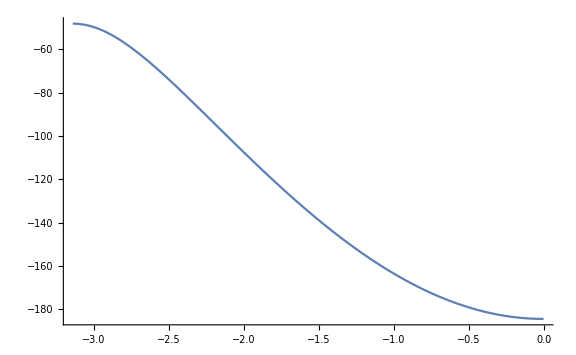

```mathematica
Plot[mov,{θ1,-180°,0°},ImageSize->Large,PlotRange->All,AxesOrigin->{0,0}]
```

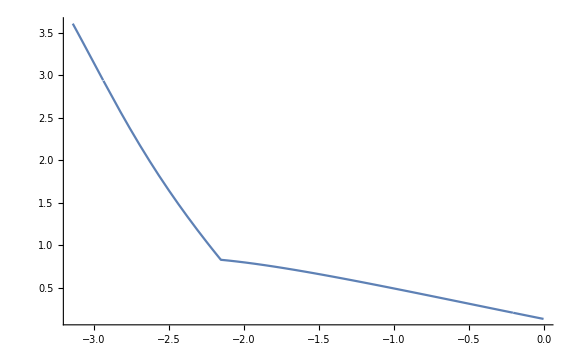

```mathematica
Plot[somma1-θ1,{θ1,-180°,0°},ImageSize->Large,PlotRange->All,AxesOrigin->{0,0}]
```

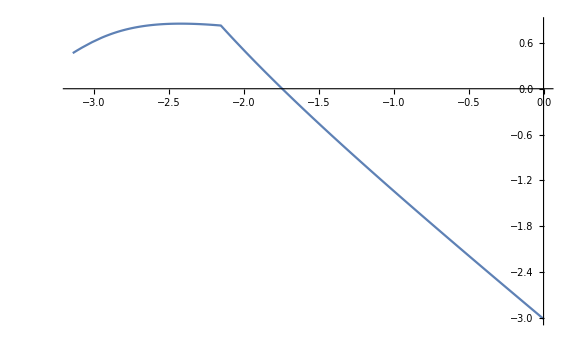

```mathematica
Plot[somma2-θ1,{θ1,-180°,0°},ImageSize->Large,PlotRange->All,AxesOrigin->{0,0}]
```

C’è una strana non linearità, provo a plottare entrambi i valori

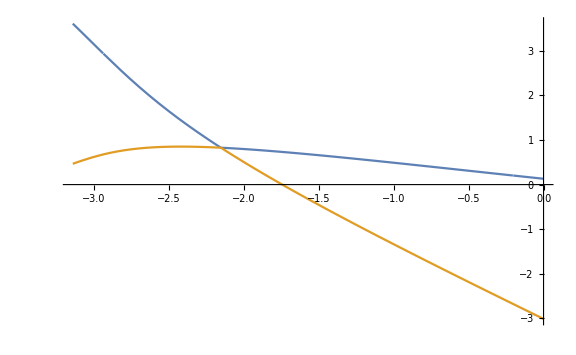

```mathematica
Plot[{somma1-θ1,somma2-θ1},{θ1,-180°,0°},ImageSize->Large,PlotRange->All,AxesOrigin->{0,0}]
```

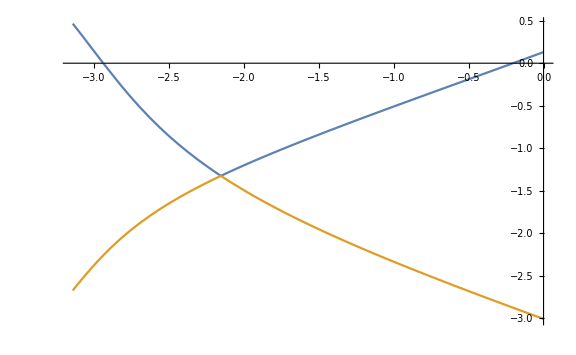

```mathematica
Plot[{somma1,somma2},{θ1,-180°,0°},ImageSize->Large,PlotRange->All,AxesOrigin->{0,0}]
```

Il punto di intersezione si ha proprio per sin(θ1) = - √(h3^2+mov^2)/l1^2

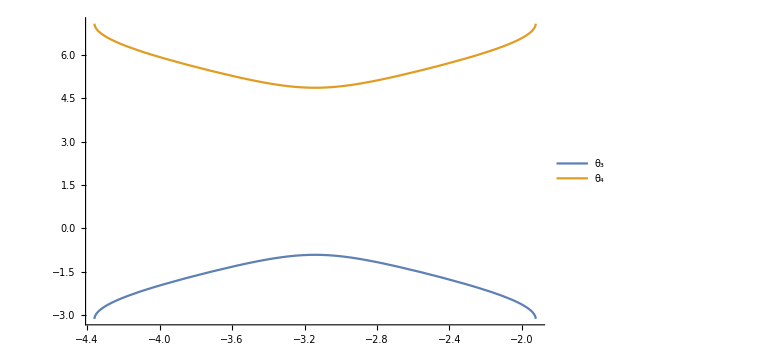

```mathematica
t3=-ArcCos[(-2 l2-2 yinf Cos[alpha+beta]+2 r1 Sin[beta]+2 xinf Sin[alpha+beta]-√(d0^2-4 h3^2+4 d0 l1 Cos[θ1]+4 l1^2 Cos[θ1]^2+4 l1^2 Sin[θ1]^2))/(2 l3)];
Plot[{t3,2Pi-alpha-beta-t3},{θ1,-360°,0°},ImageSize->Large,AxesOrigin->{0,0},PlotRange->All,PlotLegends->{"θ_3","θ_4"}]
```

Gomito basso

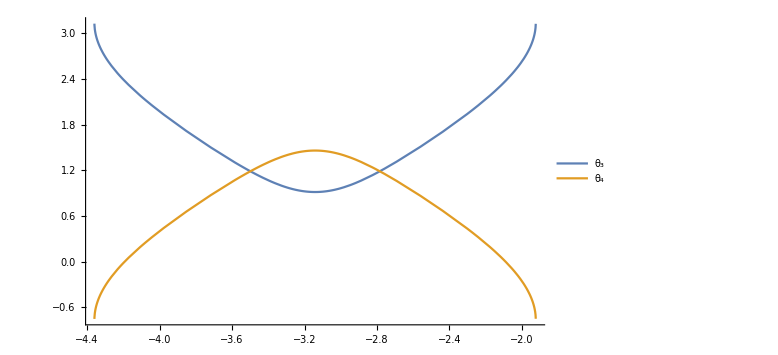

```mathematica
t3=ArcCos[(-2 l2-2 yinf Cos[alpha+beta]+2 r1 Sin[beta]+2 xinf Sin[alpha+beta]-√(d0^2-4 h3^2+4 d0 l1 Cos[θ1]+4 l1^2 Cos[θ1]^2+4 l1^2 Sin[θ1]^2))/(2 l3)];
Plot[{t3,3Pi/2-alpha-beta-t3},{θ1,-360°,0°},ImageSize->Large,AxesOrigin->{0,0},PlotRange->All,PlotLegends->{"θ_3","θ_4"}]
```

Gomito alto (ok!)

Vado a risolvere nuovamente l’equazione

```mathematica
Solve[somma1==gamma-Pi/3,θ1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ1→-2.06791+0. ⅈ}}

```mathematica
Solve[somma2==gamma-Pi/3,θ1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{}

```mathematica
-2.06/Degree
```

-118.029

```mathematica
With[{θ1=-2.067910204516095},Evaluate[{somma1-θ1,t3,3Pi/2-alpha-beta-t3}]]
```

{0.811273,2.43244,-0.058796}

```mathematica
With[{θ1=-2.067910204516095},Evaluate[{somma1-θ1,t3,3Pi/2-alpha-beta-t3}/Degree]]
```

{46.4825,139.369,-3.36876}

Ho trovato gli angoli di giunto tali per cui il robot sta chiuso a sfera.